```mathematica
f[x_]:=1/(1+25 x^2);
```

```mathematica
(*Lagrange Interpolation*)
```

```mathematica
n=10;
For[i=0,i≤n,i++,
For[{j=0,L[i,x]=1},j≤n,j++,If[j≠i,L[i,x]=L[i,x]*(x-x[j])/(x[i]-x[j])]]]
For[j=0,j≤n,j++,x[j]=-1+(2 j)/n]
Lagrange=Sum[f[x[i]]*L[i,x],{i,0,n}]//N//Expand;
Plot[{Lagrange,f[x]},{x,-1,1},PlotRange->All,PlotLegends->{"Lagrange interpolation .\n polynomial with.\n degree "<>ToString[n],f[x]}]
```

```mathematica
(*Discrete Linear Interpolation*)
```

```mathematica
n=10;
For[j=0,j≤n,j++,y[j]=-1+(2 j)/n]
g[x_]:=For[j=0,j≤n,j++,If[y[j]≤x<y[j+1],Return[(f[y[j]]*n)/2 (y[j+1]-x)+(f[y[j+1]]*n)/2(x-y[j])]]];
```

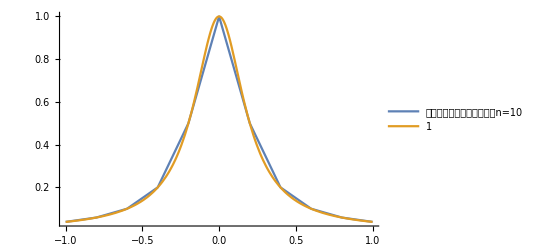

```mathematica
Plot[{g[x],f[x]},{x,-1,1},PlotRange->All,PlotLegends->{"分段线性插值，等距节点取n="<>ToString[n],f[x]}]
```

```mathematica
(*Cubic Hermite Spline*)
```

```mathematica
list=Differences[f/@Table[-1+(2 i)/n,{i,0,n}],2]*3;
```

```mathematica
A=2*IdentityMatrix[n-1];
For[i=1,i<n,i++,
For[j=1,j<n,j++,If[i==j+1||j==i+1,A[[i,j]]=1/2]]]
```

```mathematica
(*Thomas Method*)
```

```mathematica
u[1]=A[[1,1]];
For[i=2,i<n,i++,l[i]=A[[i,i-1]]/u[i-1];u[i]=A[[i,i]]-l[i] A[[i-1,i]]]
l[1]=list[[1]];
For[i=2,i<n,i++,l[i]=list[[i]]-l[i] l[i-1]]
M={l[n-1]/u[n-1]};
For[i=n-2,i≥1,i--,M=Insert[M,(l[i]-A[[i,i+1]] M[[1]])/u[i],1]]
```

```mathematica
h[x_]:=For[j=0,j<n,j++,If[y[j]≤x<y[j+1],Return[n/12*(M[[j+1]] (y[j+1]-x)^3+M[[j+2]] (y[j]-x)^3+(6 f[y[j]]-(4 M[[j+1]])/n^2)(y[j+1]-x)+(6 f[y[j+1]]-(4 M[[j+2]])/n^2)(x-y[j]))]]];
```

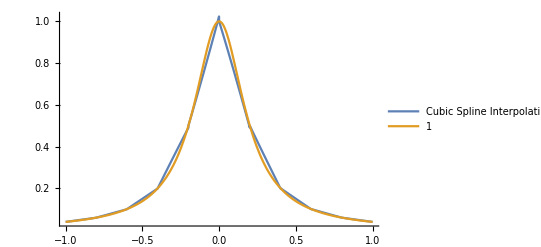

```mathematica
Plot[{h[x],f[x]},{x,-1,1},PlotRange->All,PlotLegends->{"Cubic Spline Interpolating function \n with "<>ToString[n]<>" equally spaced nodes",f[x]}]
```